## Método y f(r)

```mathematica
Clear[coord,metric,einstein,t,r,Θ,ϕ];
n=4;
fbardeen[r_,m_,q_] :=1-(2*m*r^2)/((r^2 + q^2)^(3/2));
fvaidya[r_,m_,u_]:= 1-(2*m[u])/r;
fschwarzschild[r_,m_]:=1-(2*m)/r;
fhayward[r_,m_,a_]:=1-(2*m*r^2)/(r^3 + 2*m*a^2);
todo[coord_,metric_]:=Module[{n=4,inversemetric,affine,listaffine,tableaffine,riemann,listriemann,tableriemann,ricci,listricci,tablericci,einstein,listeinstein,tableeinstein,scalar,ricciScalar,riemannScalar},
Clear[inversemetric,affine,listaffine,tableaffine,riemann,listriemann,tableriemann,ricci,listricci,tablericci,einstein,listeinstein,tableeinstein,scalar,ricciScalar,riemannScalar];
inversemetric=Simplify[Inverse[metric]];
affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]] ]+D[metric[[s,k]],coord[[j]] ]-D[metric[[j,k]],coord[[s]] ]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}] ];
listaffine=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}];
tableaffine=TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}];
riemann=Simplify[Table[D[affine[[i,j,l]],coord[[k]] ]-D[affine[[i,j,k]],coord[[l]] ]+Sum[affine[[s,j,l]] affine[[i,k,s]]-affine[[s,j,k]] affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}] ];
listriemann=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}] ,{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}];
tableriemann=TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}];
ricci=Simplify[Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}] ];
listricci=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}] ,{j,1,n},{l,1,j}];
tablericci=TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}];
scalar=Simplify[Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}] ];
ricciScalar=Simplify[Sum[inversemetric[[i1,j1]]*inversemetric[[j2,i2]]*ricci[[j1,j2]]*ricci[[i1,i2]],{i1,1,n},{i2,1,n},{j1,1,n},{j2,1,n}] ];
riemannScalar=Simplify[Sum[riemann[[i1,j1,k1,l1]] metric[[i1,i2]] inversemetric[[j1,j2]] inversemetric[[k1,k2]] inversemetric[[l1,l2]] riemann[[i2,j2,k2,l2]],{i1,1,n},{j1,1,n},{k1,1,n},{l1,1,n},{i2,1,n},{j2,1,n},{k2,1,n},{l2,1,n}]];einstein=Simplify[ricci-1/2*scalar*metric];
listeinstein=Table[If[UnsameQ[einstein[[j,l]],0],{ToString[G[j,l]],einstein[[j,l]]}] ,{j,1,n},{l,1,j}];
tableeinstein=TableForm[Partition[DeleteCases[Flatten[listeinstein],Null],2],TableSpacing->{2,2}];
Return[{affine,tableaffine,riemann,tableriemann,ricci,tablericci,einstein,tableeinstein,scalar,ricciScalar,riemannScalar}]];
(*affine = 1, tableaffine = 2,riemann = 3,tableriemann = 4,ricci = 5,tablericci = 6,einstein = 7,tableeinstein = 8,scalar = 9,ricciScalar = 10,riemannScalar = 11*)
```

## General Schwarzschild-like metric

```mathematica
coord = {t,r,θ,ϕ};
genSchMetric = {{-fschwarzschild[r,m[r]],0,0,0},{0,fschwarzschild[r,m[r]]^-1,0,0},{0,0,r^2,0},{0,0,0,r^2*Sin[θ]^2}};
invGenSchMetric =Simplify[Inverse[genSchMetric]];genSchwarzschild=todo[coord,genSchMetric];
```

```mathematica
Simplify[genSchwarzschild[[7]][[1,1]]*invGenSchMetric[[1,1]]]
```

-(2 m'[r])/r^2

```mathematica
Simplify[genSchwarzschild[[7]][[2,2]]*invGenSchMetric[[2,2]]]
```

-(2 m'[r])/r^2

```mathematica
Simplify[genSchwarzschild[[7]][[3,3]]*invGenSchMetric[[3,3]]]
```

-m''[r]/r

```mathematica
Simplify[genSchwarzschild[[7]][[4,4]]*invGenSchMetric[[4,4]]]
```

-m''[r]/r

## Schwarzschild

```mathematica
coord = {t,r,θ,ϕ};
schMetric = {{-fschwarzschild[r,m[r]],1,0,0},{1,0,0,0},{0,0,r^2,0},{0,0,0,r^2*Sin[θ]^2}};
invSchMetric =Simplify[Inverse[schMetric]];schwarzschild=todo[coord,schMetric];
```

```mathematica
schwarzschild[[8]]
```

G[1, 1] | (2 (r-2 m[r]) m'[r])/r^3
G[2, 1] | -(2 m'[r])/r^2
G[3, 3] | -r m''[r]
G[4, 4] | -r Sin[θ]^2 m''[r]

```mathematica
schwarzschild[[11]]
```

(48 m^2)/r^6

## Vaidya

```mathematica
coord = {u,r,θ,ϕ};
vaidMetric = {{-fschwarzschild[r,m[u]],-1,0,0},{-1,0,0,0},{0,0,r^2,0},{0,0,0,r^2*Sin[θ]^2}};
invVaidMetric =Simplify[Inverse[vaidMetric]];vaidya=todo[coord,vaidMetric];
```

```mathematica
invVaidMetric//MatrixForm
```

(0 | -1 | 0 | 0
-1 | 1-(2 m[u])/r | 0 | 0
0 | 0 | 1/r^2 | 0
0 | 0 | 0 | Csc[θ]^2/r^2)

```mathematica
vaidya[[8]]
```

G[1, 1] | -(2 m'[u])/r^2

## Bardeen

```mathematica
coord = {t,r,θ,ϕ};
bardMetric = {{-fbardeen[r,m,g],0,0,0},{0,fbardeen[r,m,g]^-1,0,0},{0,0,r^2,0},{0,0,0,r^2*Sin[θ]^2}};
invBardMetric =Simplify[Inverse[bardMetric]];bardeen=todo[coord,bardMetric];
```

```mathematica
Series[fbardeen[r,m,g],{r,∞,4}]
```

```mathematica
1-(2 m)/r+(3 g^2 m)/r^3+O[1/r]^5
```

1-(2 m)/r+(3 g^2 m)/r^3+O[1/r]^5

```mathematica
Series[fbardeen[r,m,g],{r,0,3}]
```

1-(2 (√(g^2) m) r^2)/g^4+O[r]^4

```mathematica
Simplify[bardeen[[7]][[1,1]]*invBardMetric[[1,1]]]
```

-(6 g^2 m)/((g^2+r^2)^(5/2))

```mathematica
Simplify[bardeen[[7]][[2,2]]*invBardMetric[[2,2]]]
```

-(6 g^2 m)/((g^2+r^2)^(5/2))

```mathematica
Simplify[bardeen[[7]][[3,3]]*invBardMetric[[3,3]]]
```

(-6 g^4 m+9 g^2 m r^2)/((g^2+r^2)^(7/2))

```mathematica
Simplify[bardeen[[7]][[4,4]]*invBardMetric[[4,4]]]
```

(-6 g^4 m+9 g^2 m r^2)/((g^2+r^2)^(7/2))

```mathematica
Simplify[D[(2*m*r^3)/((r^2 + g^2)^(3/2)),{r,1}]*1/r^2]
```

(6 g^2 m)/((g^2+r^2)^(5/2))

```mathematica
Simplify[D[(2*m*r^3)/((r^2 + g^2)^(3/2)),{r,1}]*2/r]
```

(12 g^2 m r)/((g^2+r^2)^(5/2))

```mathematica
Simplify[D[(2*m*r^3)/((r^2 + g^2)^(3/2)),{r,2}]]
```

(6 m (2 g^4 r-3 g^2 r^3))/((g^2+r^2)^(7/2))

```mathematica
bardeen[[9]]
```

(6 g^2 m (4 g^2-r^2))/((g^2+r^2)^(7/2))

```mathematica
bardeen[[10]]
```

(18 g^4 m^2 (8 g^4-4 g^2 r^2+13 r^4))/((g^2+r^2)^7)

```mathematica
bardeen[[11]]
```

(12 m^2 (8 g^8-4 g^6 r^2+47 g^4 r^4-12 g^2 r^6+4 r^8))/((g^2+r^2)^7)

## Hayward - Static

```mathematica
coord = {t,r,θ,ϕ};
hayMetric = {{-fhayward[r,m,L],0,0,0},{0,fhayward[r,m,L]^-1,0,0},{0,0,r^2,0},{0,0,0,r^2*Sin[θ]^2}};
invHayMetric =Simplify[Inverse[hayMetric]];hayward=todo[coord,hayMetric];
```

```mathematica
Series[fhayward[r,m,a],{r,∞,4}]
```

1-(2 m)/r+(4 a^2 m^2)/r^4+O[1/r]^5

```mathematica
hayward[[8]]
```

G[1, 1] | (12 L^2 m^2 (2 L^2 m+r^2 (-2 m+r)))/((2 L^2 m+r^3)^3)
G[2, 2] | -(12 L^2 m^2)/((2 L^2 m+r^3) (2 L^2 m+r^2 (-2 m+r)))
G[3, 3] | -(24 L^2 m^2 r^2 (L^2 m-r^3))/((2 L^2 m+r^3)^3)
G[4, 4] | -(24 L^2 m^2 r^2 (L^2 m-r^3) Sin[θ]^2)/((2 L^2 m+r^3)^3)

```mathematica
Simplify[hayward[[7]][[1,1]]*invHayMetric[[1,1]]]
```

-(12 L^2 m^2)/((2 L^2 m+r^3)^2)

```mathematica
Simplify[hayward[[7]][[2,2]]*invHayMetric[[2,2]]]
```

-(12 L^2 m^2)/((2 L^2 m+r^3)^2)

```mathematica
Simplify[hayward[[7]][[3,3]]*invHayMetric[[3,3]]]
```

-(24 L^2 m^2 (L^2 m-r^3))/((2 L^2 m+r^3)^3)

```mathematica
Simplify[hayward[[7]][[4,4]]*invHayMetric[[4,4]]]
```

-(24 L^2 m^2 (L^2 m-r^3))/((2 L^2 m+r^3)^3)

```mathematica
Simplify[D[(2*m*r^3)/(r^3 + 2*m*a^2),{r,1}]*1/r^2]
```

(12 a^2 m^2)/((2 a^2 m+r^3)^2)

```mathematica
Simplify[D[(2*m*r^3)/(r^3 + 2*m*a^2),{r,1}]*2/r]
```

(24 a^2 m^2 r)/((2 a^2 m+r^3)^2)

```mathematica
Simplify[D[(2*m*r^3)/(r^3 + 2*m*a^2),{r,2}]]
```

(48 m^2 (a^4 m r-a^2 r^4))/((2 a^2 m+r^3)^3)

```mathematica
hayward[[9]]
```

(24 L^2 m^2 (4 L^2 m-r^3))/((2 L^2 m+r^3)^3)

```mathematica
hayward[[10]]
```

(288 m^4 (8 L^8 m^2-4 L^6 m r^3+5 L^4 r^6))/((2 L^2 m+r^3)^6)

```mathematica
hayward[[11]]
```

(48 m^2 (32 L^8 m^4-16 L^6 m^3 r^3+72 L^4 m^2 r^6-8 L^2 m r^9+r^12))/((2 L^2 m+r^3)^6)

```mathematica
Series[fhayward[r,m,a],{r,0,4}]
```

1-r^2/a^2+O[r]^5

```mathematica
labels[m_]:={m=0,m<SubStar[m],m=SubStar[m],m>SubStar[m]};
len:=Length[labels[m]];
```

```mathematica
Manipulate[Plot[{fhayward[r,m4,1],fhayward[r,m1,1],fhayward[r,m2,1],fhayward[r,m3,1]},{r,0,5},PlotStyle->{Red,Blue,Orange,Green},PlotLegends->{"m=0","m<m_*","m=m_*","m>m_*"}], {m1,0.5,1.5},{m2,0.5,1.5},{m3,0.5,2.5},{m4,0,2.5}]
```

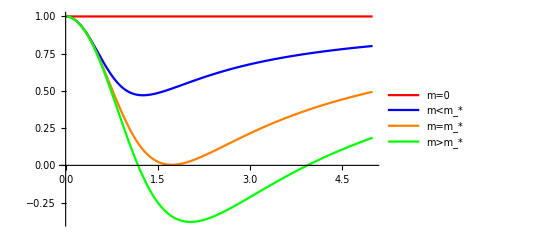

```mathematica
Plot[{fhayward[r,0,1],fhayward[r,0.5,1],fhayward[r,1.291,1],fhayward[r,2.105,1]},{r,0,5},PlotStyle->{Red,Blue,Orange,Green},PlotLegends->{"m=0","m<m_*","m=m_*","m>m_*"}]
```

```mathematica
Solve[Simplify[D[fhayward[r,m,a],{r,1}]]==0,{r}]
```

{{r→0},{r→(-2)^(2/3) a^(2/3) m^(1/3)},{r→2^(2/3) a^(2/3) m^(1/3)},{r→-(-1)^(1/3) 2^(2/3) a^(2/3) m^(1/3)}}

```mathematica
Solve[fhayward[2^(2/3) a^(2/3) m^(1/3),m,a]==0,{m}]
```

{{m→(3 √3 a)/4}}

```mathematica
Solve[fhayward[r,(3 √3)/4*a,a]==0,{r}]
```

{{r→-(√3 a)/2},{r→√3 a},{r→√3 a}}

```mathematica
Simplify[Solve[fhayward[r,m,a]==0,r]]
```

{{r→1/3 (2 m+(4 m^2)/((-27 a^2 m+8 m^3+3 √(81 a^4 m^2-48 a^2 m^4))^(1/3))+(-27 a^2 m+8 m^3+3 √(81 a^4 m^2-48 a^2 m^4))^(1/3))},{r→(2 m)/3-(2 ⅈ (-ⅈ+√3) m^2)/(3 (-27 a^2 m+8 m^3+3 √(81 a^4 m^2-48 a^2 m^4))^(1/3))+1/6 ⅈ (ⅈ+√3) (-27 a^2 m+8 m^3+3 √(81 a^4 m^2-48 a^2 m^4))^(1/3)},{r→(2 m)/3+(2 ⅈ (ⅈ+√3) m^2)/(3 (-27 a^2 m+8 m^3+3 √(81 a^4 m^2-48 a^2 m^4))^(1/3))-1/6 ⅈ (-ⅈ+√3) (-27 a^2 m+8 m^3+3 √(81 a^4 m^2-48 a^2 m^4))^(1/3)}}

```mathematica
Series[1/3 (2 m+(4 m^2)/((-27 a^2 m+8 m^3+3 √(81 a^4 m^2-48 a^2 m^4))^(1/3))+(-27 a^2 m+8 m^3+3 √(81 a^4 m^2-48 a^2 m^4))^(1/3)),{m,∞,2}]
```

2 m-a^2/(2 m)+O[1/m]^3

```mathematica
Solve[fhayward[r,m,a]==0,{m}]
```

{{m→r^3/(2 (-a^2+r^2))}}

```mathematica
Manipulate[Plot[r^3/(2 (-a^2+r^2)),{r,0,10},RegionFunction->(#2>0&),ExclusionsStyle-> Black],{a,0,1.5}]
```

## Hayward-Dynamic

```mathematica
coord = {v,r,θ,ϕ};
hayMetric2 = {{-fhayward[r,m[v],L],1,0,0},{1,0,0,0},{0,0,r^2,0},{0,0,0,r^2*Sin[θ]^2}};
invHayMetric2 =Simplify[Inverse[hayMetric2]];hayward2=todo[coord,hayMetric2];
```

```mathematica
hayward2[[8]]
```

```mathematica
invHayMetric2//MatrixForm
```

(0 | 1 | 0 | 0
1 | (r^3+2 (L^2-r^2) m[v])/(r^3+2 L^2 m[v]) | 0 | 0
0 | 0 | 1/r^2 | 0
0 | 0 | 0 | Csc[θ]^2/r^2)

```mathematica
Simplify[hayward2[[7]][[1,2]]*invHayMetric2[[2,2]]]
```

-(12 L^2 m[v]^2 (r^3+2 (L^2-r^2) m[v]))/((r^3+2 L^2 m[v])^3)